```mathematica
(*Mathematica*)
```

```mathematica
Clear[s,w]
```

```mathematica
(*First so(5)*)
s[1]={{0,1,0,0,0},
           {1,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[2]={{0,0,1,0,0},
           {0,0,0,0,0},
          {1,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[3]={{0,0,0,1,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0},
{0,0,0,0,0}};
s[4]={{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0}};
s[5]={{0,0,0,0,0},
{0,0,1,0,0},
{0,1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[10]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,1},
        { 0,0,0,1,0}};
s[9]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,1,0,0}};
s[8]={{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,1,0,0,0}};
s[7]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,1,0},
{0,0,1,0,0},
{0,0,0,0,0}};
s[6]={{0,0,0,0,0},
{0,0,0,1,0},
{0,0,0,0,0},
{0,1,0,0,0},
{0,0,0,0,0}};
(* second so(5) *)
s[11]={{0,I,0,0,0},
           {-I,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[12]={{0,0,-I,0,0},
           {0,0,0,0,0},
          {I,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[13]={{0,0,0,I,0},
{0,0,0,0,0},
{0,0,0,0,0},
{-I,0,0,0,0},
{0,0,0,0,0}};
s[14]={{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{I,0,0,0,0}};
s[15]={{0,0,0,0,0},
{0,0,I,0,0},
{0,-I,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[20]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,I},
        { 0,0,0,-I,0}};
s[19]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,I,0,0}};
s[18]={{0,0,0,0,0},
{0,0,0,0,I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,-I,0,0,0}};
s[17]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,I,0},
{0,0,-I,0,0},
{0,0,0,0,0}};
s[16]={{0,0,0,0,0},
{0,0,0,-I,0},
{0,0,0,0,0},
{0,I,0,0,0},
{0,0,0,0,0}};
(* DIAGONAL four: n-1 matrices*)
(* zero trace with normalization Sqrt[n*(n-1)/2]*)
s[21]={{1,0,0,0,0},
{0,-1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[22]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,-2,0,0},
{0,0,0,0,0},
{0,0,0,0,-1}}/Sqrt[7/2];
s[23]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,1,0,0},
{0,0,0,-3,0},
{0,0,0,0,0}}/Sqrt[6];
s[24]={{2,0,0,0,0},
{0,2,0,0,0},
{0,0,2,0,0},
{0,0,0,-3,0},
{0,0,0,0,-3}}/√30;
s[25]=IdentityMatrix[5];
```

```mathematica
p[x_]=-1+296 x^6-602 x^12-296 x^18-x^24
```

-1+296 x^6-602 x^12-296 x^18-x^24

```mathematica
r[i_]:=z/.NSolve[p[z]==0,z][[i]]
```

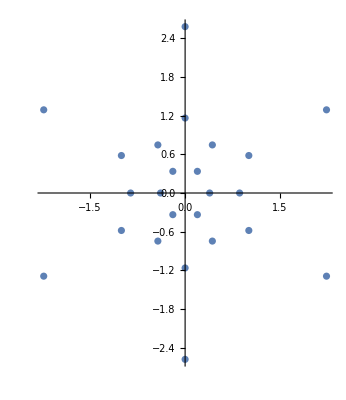

```mathematica
ComplexListPlot[Table[r[i],{i,24}]]
```

```mathematica
(*deSitter*)
```

```mathematica
f1[z_]=(285.72572719531513-281.59622269597827 ⅈ)+(67.61593234390679-3.8849084680240367 ⅈ) z-(145.45507501915057-152.55818585456095 ⅈ) z^2+(74.02603669708652+54.3439819119841 ⅈ) z^3+(24.12557540899769-108.92714625311521 ⅈ) z^4-36.1405042694867 z^5
```

(285.726-281.596 ⅈ)+(67.6159-3.88491 ⅈ) z-(145.455-152.558 ⅈ) z^2+(74.026+54.344 ⅈ) z^3+(24.1256-108.927 ⅈ) z^4-36.1405 z^5

```mathematica
(*Anti-deSitter*)
```

```mathematica
f2[z_]=N[Det[s[25]+Sum[s[i]*(z-r[i]),{i,24}]]]//Chop
```

(343.098-123.638 ⅈ)-(73.0414-165.54 ⅈ) z-(187.208-59.652 ⅈ) z^2+(78.1645-28.3751 ⅈ) z^3+(84.3434-59.4619 ⅈ) z^4-55.2416 z^5

```mathematica
f[z_]=ExpandAll[z^2*f1[z]/f2[z]]
```

((285.726-281.596 ⅈ) z^2)/((343.098-123.638 ⅈ)-(73.0414-165.54 ⅈ) z-(187.208-59.652 ⅈ) z^2+(78.1645-28.3751 ⅈ) z^3+(84.3434-59.4619 ⅈ) z^4-55.2416 z^5)+((67.6159-3.88491 ⅈ) z^3)/((343.098-123.638 ⅈ)-(73.0414-165.54 ⅈ) z-(187.208-59.652 ⅈ) z^2+(78.1645-28.3751 ⅈ) z^3+(84.3434-59.4619 ⅈ) z^4-55.2416 z^5)-((145.455-152.558 ⅈ) z^4)/((343.098-123.638 ⅈ)-(73.0414-165.54 ⅈ) z-(187.208-59.652 ⅈ) z^2+(78.1645-28.3751 ⅈ) z^3+(84.3434-59.4619 ⅈ) z^4-55.2416 z^5)+((74.026+54.344 ⅈ) z^5)/((343.098-123.638 ⅈ)-(73.0414-165.54 ⅈ) z-(187.208-59.652 ⅈ) z^2+(78.1645-28.3751 ⅈ) z^3+(84.3434-59.4619 ⅈ) z^4-55.2416 z^5)+((24.1256-108.927 ⅈ) z^6)/((343.098-123.638 ⅈ)-(73.0414-165.54 ⅈ) z-(187.208-59.652 ⅈ) z^2+(78.1645-28.3751 ⅈ) z^3+(84.3434-59.4619 ⅈ) z^4-55.2416 z^5)-(36.1405 z^7)/((343.098-123.638 ⅈ)-(73.0414-165.54 ⅈ) z-(187.208-59.652 ⅈ) z^2+(78.1645-28.3751 ⅈ) z^3+(84.3434-59.4619 ⅈ) z^4-55.2416 z^5)

```mathematica
w=z/.NSolve[f[z]==0,z]
```

{0.527242-3.01904 ⅈ,-1.40956-0.903118 ⅈ,1.53954-0.393266 ⅈ,0.965753+0.863705 ⅈ,-0.95542+0.437728 ⅈ,0.,0.}

```mathematica
max=Max[Norm/@w]+1.5
```

4.56473

```mathematica
ga=ComplexPlot[f[z],{z,-max-I*(max-0.5),max+I*(max-0.5)},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100];
```

```mathematica
gb=ComplexPlot3D[f[z],{z,-max-I*(max-0.5),max+I*(max-0.5)},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100,ViewPoint->Above];
```

```mathematica
(*g1=JuliaSetPlot[f[x],x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False,PlotRange->All];
g2=ListPlot[JuliaSetPoints[f[x],x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All];*)
Export["Julia_hermanrings2_SU5_deSitter_anti_deSitter_6Dodecahedron_Polynomial_grid.jpg",GraphicsGrid[{{gb}, 
 {ga}},ImageSize->4000]]
```

Julia_hermanrings2_SU5_deSitter_anti_deSitter_6Dodecahedron_Polynomial_grid.jpg

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Sept 20026© *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 512) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=f[nz]/2;
		
    
		++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]],Abs[Arg[nz]-Arg[nz]^3/3]]
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-max+0.0001,max,1000},{-max-0.5,max-0.5,1000}}];
```

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction→"Rainbow",Background→Black,ViewPoint→Above,ImageSize->{2000,2000}];
```

```mathematica
Export["j_1000_hermanrings2_SU5_deSitter_anti_deSitter_7Docecahedron_Polynomial_In_Out_monitor_g1.jpg",g1]
```

j_1000_hermanrings2_SU5_deSitter_anti_deSitter_7Docecahedron_Polynomial_In_Out_monitor_g1.jpg

```mathematica
g2=ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction-> (Hue[1.75*#]&),ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_hermanrings2_SU5_deSitter_anti_deSitter_7Docecahedron_Polynomial_In_Out_monitor_g2.jpg",g2]
```

j_1000_hermanrings2_SU5_deSitter_anti_deSitter_7Docecahedron_Polynomial_In_Out_monitor_g2.jpg

```mathematica
colortab=Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]];
```

```mathematica
Length[%]
```

542

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/542,1,Ceiling[542*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_hermanrings2_SU5_deSitter_anti_deSitter_7Docecahedron_Polynomial_In_Out_monitor_g3.jpg",g3]
```

j_1000_hermanrings2_SU5_deSitter_anti_deSitter_7Docecahedron_Polynomial_In_Out_monitor_g3.jpg

```mathematica
Export["Julia_hermanrings2_1000_SU5_deSitter_anti_deSitter_7Docecahedron_Polynomial_grid.jpg",GraphicsGrid[{{ga,g2}, 
 {g3,g1}},ImageSize->4000]]
```

Julia_hermanrings2_1000_SU5_deSitter_anti_deSitter_7Docecahedron_Polynomial_grid.jpg

```mathematica
(*end*)
```